```mathematica
u[x_, y_, z_] := Sqrt[x^2+y^2+z^2]
```

```mathematica
Grad[Log[u[x, y, z]], {x, y,z}]
```

{x/(x^2+y^2+z^2),y/(x^2+y^2+z^2),z/(x^2+y^2+z^2)}

```mathematica
{{-1/2,-Sqrt[3]/2},{Sqrt[3]/2,-1/2}}.{{-1/2,-Sqrt[3]/2},{Sqrt[3]/2,-1/2}}.{{-1/2,-Sqrt[3]/2},{Sqrt[3]/2,-1/2}}
```

{{1,0},{0,1}}

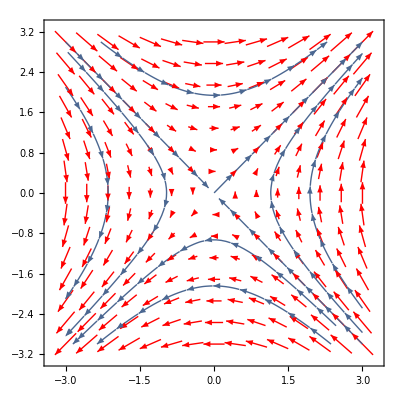

```mathematica
VectorPlot[{y,x},{x,-3,3},{y,-3,3},VectorStyle->Red,StreamPoints->10]
```

```mathematica
StreamPlot[{x/(x^2+y^2)^(3/2),y/(x^2+y^2)^(3/2)},{x,-3,3},{y,-3,3}, Mesh->0.1]
```

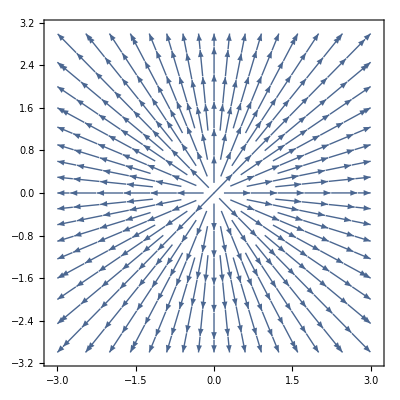

```mathematica
vec[x0_, y0_, x_, y_] := 1/((x-x0)^2+(y-y0)^2) *{x - x0, y-y0} / ((x-x0)^2+(y-y0)^2)
```

```mathematica
vec[0,0,1,1]
```

{1/4,1/4}

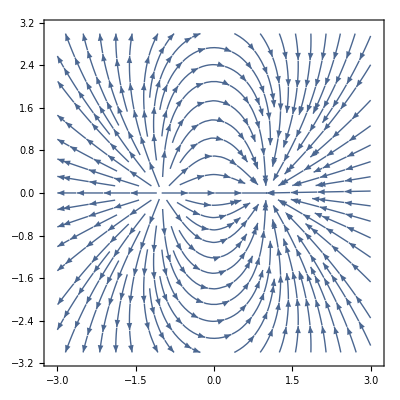

```mathematica
StreamPlot[vec[-1,0,x,y]-vec[1,0,x,y],{x,-3,3},{y,-3,3}]
```

```mathematica
ListDensityPlot[{{1,1,1,1},{1,2,1,2},{1,1,3,1}},PlotTheme->"Detailed",Mesh->All]
```

-Graphics-

```mathematica
ListDensityPlot[{{0, 0, 1}, {1, 0, 0}, {0, 1, -1}, {1, 1, 1}}, Mesh->All]
```

-Graphics-

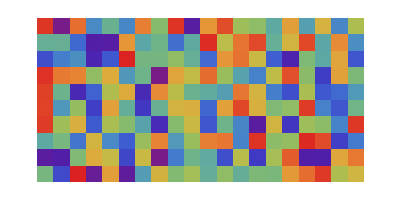

```mathematica
ArrayPlot[RandomReal[1,{10,20}],ColorFunction->"Rainbow"]
```

```mathematica
e[x_,y_] := {y, 2x}
```

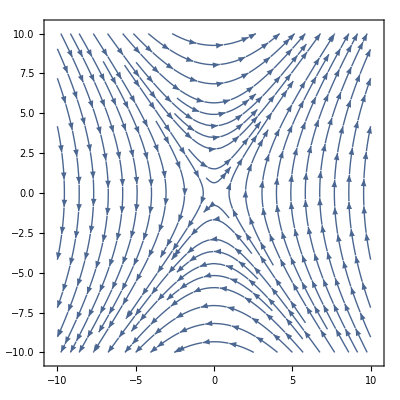

```mathematica
StreamPlot[e[x,y], {x, -10,10}, {y, -10,10}]
```

```mathematica
filename = "D:\Desktop\ChargeDistribution\out.txt"
```

D:\Desktop\ChargeDistribution\out.txt

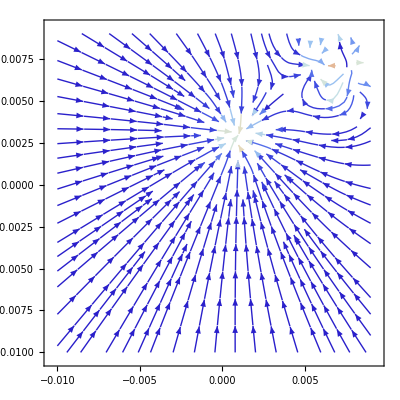

```mathematica
ListStreamPlot[ToExpression[Import[filename]], StreamColorFunction->"ThermometerColors"]
```

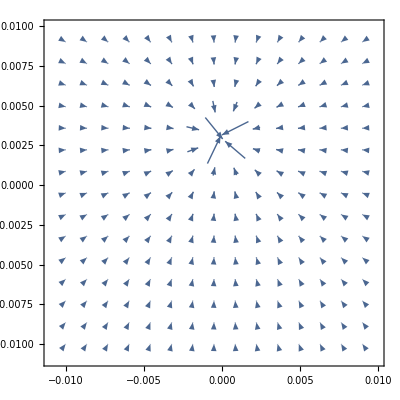

```mathematica
ListVectorPlot[ToExpression[Import[filename]]]
```

```mathematica
pointfile = "D:\Desktop\ChargeDistribution\points.txt"
```

D:\Desktop\ChargeDistribution\points.txt

```mathematica
ListPointPlot3D[ToExpression[Import[pointfile]],Axes->True, BoxRatios->Automatic]
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
normvec = "D:/Desktop/ChargeDistribution/normvec.txt"
```

D:/Desktop/ChargeDistribution/normvec.txt

```mathematica
ToExpression[Import[normvec]]
```

{{-0.075,-0.075,-0.075},{0.494233,0.0349936,0.868625},{-0.075,-0.075,-0.065},{0.494233,0.0349936,0.868625},8184,{0.075,0.075,0.065},{-0.40999,0.035509,-0.911399},{0.075,0.075,0.075},{-0.40999,0.035509,-0.911399}}
 |  |  |  |

```mathematica
ListVectorPlot3D[ToExpression[Import[normvec]]]
```

Visualization`Core`ListVectorPlot3D::vfldata: {{-0.075,-0.075,-0.075},{0.494233,0.0349936,0.868625},{-0.075,-0.075,-0.065},{0.494233,0.0349936,0.868625},{-0.075,-0.075,-0.055},«42»,{0.494233,0.0349936,0.868625},{-0.075,-0.065,0.005},{0.494233,0.0349936,0.868625},«8142»} is not a valid vector field dataset or a valid list of datasets.

ListVectorPlot3D[{{-0.075,-0.075,-0.075},{0.494233,0.0349936,0.868625},{-0.075,-0.075,-0.065},{0.494233,0.0349936,0.868625},8185,{-0.40999,0.035509,-0.911399},{0.075,0.075,0.075},{-0.40999,0.035509,-0.911399}}]
 |  |  |  |